```mathematica
DD[n_,k_] := Sum[ DD[n/j,k-1],{j,1,n}]
DD[n_,0] := 1
DD[100,4]
3575
PP[n_, k_, a_ ] := Sum[ a N[ MangoldtLambda[j]/Log[j]]( 1/(k!) + PP[n/j, k+1,a]),{j,2,n}]
PP[100,1,4]
P2[ n_, a_ ] := PP[n,1,a]
P2[ 100,3]
DD[100,3]
P2[100, I]
P3[n_, k_ ] := P2[n,k]/k
DiscretePlot[Re[ P3[j,I]+P3[j,-I]],{j,2,100}]
```

```mathematica
QQ[n_, k_, a_ ] := Sum[ a ( 1/k - QQ[n/j, k+1,a]),{j,2,n}]
Q2[ n_, a_ ] := QQ[n,1,a]
Q3[n_, k_ ] := Q2[n,k]/k
Q4[n_, k_ ] := (Q3[n,1+k] + Q3[n,1-k])/2
```

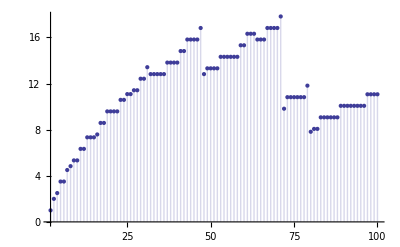

```mathematica
DiscretePlot[ Re[Q4[j,1+I]],{j,2,100}]
```

```mathematica
Table[Q4[n,1+I]-Q4[n-1,1+I],{n,2,100}]
```

{1,1,1/2,1,0,1,1/3+(2 ⅈ)/3,1/2,0,1,2 ⅈ,1,0,0,1/4+ⅈ/2,1,2 ⅈ,1,2 ⅈ,0,0,1,0,1/2,0,1/3+(2 ⅈ)/3,2 ⅈ,1,4 ⅈ,1,-3/5+(2 ⅈ)/5,0,0,0,-ⅈ,1,0,0,0,1,4 ⅈ,1,2 ⅈ,2 ⅈ,0,1,-4,1/2,2 ⅈ,0,2 ⅈ,1,0,0,0,0,0,1,-4 ⅈ,1,0,2 ⅈ,-1/2+ⅈ/3,0,4 ⅈ,1,2 ⅈ,0,4 ⅈ,1,-8,1,0,2 ⅈ,2 ⅈ,0,4 ⅈ,1,-4,1/4+ⅈ/2,0,1,-4 ⅈ,0,0,0,0,1,-4 ⅈ,0,2 ⅈ,0,0,0,0,1,2 ⅈ,2 ⅈ,-ⅈ}